## Relevant Computation for the PRL submission

## Efficienze intrinseche e totali e risoluzione

```mathematica
resol[e_,stat_,syst_]:=stat Sqrt[ e/10] + syst e/10;
resolK[e_]:=resol[e,1.27,1.0 ];
resolI[e_]:=resol[e,3.3, 0.2 ];
resolB[e_]:= resol[e, 0.0 ,2.0 ]; 


gK[e_]:= (1+ Erf[ (e-4.5)/( Sqrt[2] resolK[e] ) ])/2.
gI[e_]:= (1+ Erf[ (e-15)/( Sqrt[2] resolI[e] ) ])/2.;
gB[e_]:= (1+ Erf[ (e+me-10)/( Sqrt[2] resolB[e+me] )])/2.;


GK[e_,Ei_]:=  1/(√(2 Pi)resolK[e])Exp[-(Ei-e)^2/(2 (resolK[e]^2))];
GI[e_, Ei_]:= 1/(√(2 Pi)resolI[e])Exp[-(Ei-e)^2/(2 (resolI[e]^2))];
GB[e_, Ei_]:= 1/(√(2 Pi)resolB[e+me])Exp[-(Ei-e-me)^2/(2 (resolB[e+me]^2))];

eIMB=15.;

etaK[e_]:=0.93 ( 1 -0.2/e - (2.5/e)^2 ) HeavisideTheta[e-2.6];
etaI[e_]:=( 0.379 (e/eIMB-1)- 6 10^-3 (e/eIMB-1)^4+ 10^-3 (e/eIMB-1)^5 ) HeavisideTheta[e-eIMB];
etaB[e_]:= 1.0;

effK[e_]:= gK[e] etaK[e];
effI[e_]:= gI[e] etaI[e];
effB[e_]:= gB[e] etaB[e];
```

## Useful physical constants and conversione factor

```mathematica
c=29979245800;
```

```mathematica
h=6.62607015/(1.602*10^-19)*10^-6*10^-34;
```

```mathematica
MevBarn=389.379372;
```

```mathematica
Barncmsquared=10^-24;
```

```mathematica
MeVbarn:=389.379372
```

```mathematica
Subscript[M, sun]=2.1955*10^60 me;
```

```mathematica
d=(51.4/50)*1.543*10^23;
```

```mathematica
kA=1/(4*Pi*d^2)*c/(h c)^3*Subscript[M, sun]/mn*8*Pi;
```

```mathematica
kC=1/(4*Pi*d^2)*c/(h c)^3 Pi*4*Pi;
```

```mathematica
Subscript[τ, d]=0.035
```

0.035

```mathematica
flife=0.9055
```

0.9055

## The likelihood for SN1987A data

```mathematica
loglikelihoodKK[R_, ζ_,T0_,a_,f_,t0_,td_]:= Re[2*(SfunctionAKK[0.6T0]*ζ*a*GfunctionAKK[t0/a]+R^2*f*GfunctionCKK[T0,t0/f]-Log[signalAKK1[0.6*T0]*ζ*FcalligraphicA[td,t0,a]+signalCKK1[T0*(FcalligraphicC[td,t0,f])^(1/4)]*R^2+0.5*10^-5]-Log[signalAKK2[0.6*T0]*ζ*FcalligraphicA[0.157+td-0.05,t0,a]+signalCKK2[T0*(FcalligraphicC[0.157-0.05+td,t0,f])^(1/4)]*R^2+2.7*10^-4]-Log[signalAKK3[0.6*T0]*ζ*FcalligraphicA[0.353-0.05+td,t0,a]+signalCKK3[T0*(FcalligraphicC[0.353-0.05+td,t0,f])^(1/4)]*R^2+1.2*10^-2]-Log[signalAKK4[0.6*T0]*ζ*FcalligraphicA[0.374-0.05+td,t0,a]+signalCKK4[T0*(FcalligraphicC[0.374-0.05+td,t0,f])^(1/4)]*R^2+1.4*10^-3]-Log[signalAKK5[0.6*T0]*ζ*FcalligraphicA[0.557-0.05+td,t0,a]+signalCKK5[T0*(FcalligraphicC[0.557-0.05+td,t0,f])^(1/4)]*R^2+2.65*10^-4]-Log[signalAKK6[0.6*T0]*ζ*FcalligraphicA[0.736-0.05+td,t0,a]+signalCKK6[T0*(FcalligraphicC[0.736-0.05+td,t0,f])^(1/4)]*R^2+3.95*10^-2]-Log[signalAKK7[0.6*T0]*ζ*FcalligraphicA[1.591-0.05+td,t0,a]+signalCKK7[T0*(FcalligraphicC[1.591-0.05+td,t0,f])^(1/4)]*R^2+2.5*10^-6]-Log[signalAKK8[0.6*T0]*ζ*FcalligraphicA[1.778-0.05+td,t0,a]+signalCKK8[T0*(FcalligraphicC[1.778-0.05+td,t0,f])^(1/4)]*R^2+0.5*10^-5]-Log[signalAKK9[0.6*T0]*ζ*FcalligraphicA[1.965-0.05+td,t0,a]+signalCKK9[T0*(FcalligraphicC[1.965-0.05+td,t0,f])^(1/4)]*R^2+0.5*10^-5]-Log[signalAKK10[0.6*T0]*ζ*FcalligraphicA[9.269-0.05+td,t0,a]+signalCKK10[T0*(FcalligraphicC[9.269-0.05+td,t0,f])^(1/4)]*R^2+2.1*10^-3]-Log[signalAKK11[0.6*T0]*ζ*FcalligraphicA[10.483-0.05+td,t0,a]+signalCKK11[T0*(FcalligraphicC[10.483-0.05+td,t0,f])^(1/4)]*R^2+2*10^-4]-Log[signalAKK12[0.6*T0]*ζ*FcalligraphicA[12.489-0.05+td,t0,a]+signalCKK12[T0*(FcalligraphicC[12.489-0.05+td,t0,f])^(1/4)]*R^2+1.6*10^-3]-Log[signalAKK13[0.6*T0]*ζ*FcalligraphicA[17.691-0.05+td,t0,a]+signalCKK13[T0*(FcalligraphicC[17.691-0.05+td,t0,f])^(1/4)]*R^2+3.65*10^-2]-Log[signalAKK14[0.6*T0]*ζ*FcalligraphicA[20.301-0.05+td,t0,a]+signalCKK14[T0*(FcalligraphicC[20.301-0.05+td,t0,f])^(1/4)]*R^2+2.65*10^-2]-Log[signalAKK15[0.6*T0]*ζ*FcalligraphicA[21.405-0.05+td,t0,a]+signalCKK15[T0*(FcalligraphicC[21.405-0.05+td,t0,f])^(1/4)]*R^2+0.9*10^-2]-Log[signalAKK16[0.6*T0]*ζ*FcalligraphicA[23.864-0.05+td,t0,a]+signalCKK16[T0*(FcalligraphicC[23.864-0.05+td,t0,f])^(1/4)]*R^2+3.65*10^-2])];
```

```mathematica
loglikelihoodI[R_, ζ_,T0_,a_,f_,t0_,td_]:= Re[2*(flife*(SfunctionAI[0.6T0]*ζ*a*GfunctionAI[t0/a]+R^2*f*GfunctionCI[T0,t0/f]-Subscript[τ, d]*(SfunctionAI[0.6T0]*ζ*FcalligraphicA[Subscript[τ, d]/2+td,t0,a]+R^2*SfunctionCI[T0*(FcalligraphicC[td+Subscript[τ, d]/2,t0,f])^(1/4)]+SfunctionAI[0.6T0]*ζ*FcalligraphicA[0.412+td+Subscript[τ, d]/2,t0,a]+R^2*SfunctionCI[T0*(FcalligraphicC[0.412+td+Subscript[τ, d]/2,t0,f])^(1/4)]+SfunctionAI[0.6T0]*ζ*FcalligraphicA[0.650+td+Subscript[τ, d]/2,t0,a]+R^2*SfunctionCI[T0*(FcalligraphicC[0.650+td+Subscript[τ, d]/2,t0,f])^(1/4)]+SfunctionAI[0.6T0]*ζ*FcalligraphicA[1.141+td+Subscript[τ, d]/2,t0,a]+R^2*SfunctionCI[T0*(FcalligraphicC[1.141+td+Subscript[τ, d]/2,t0,f])^(1/4)]+SfunctionAI[0.6T0]*ζ*FcalligraphicA[1.562+td+Subscript[τ, d]/2,t0,a]+R^2*SfunctionCI[T0*(FcalligraphicC[1.562+td+Subscript[τ, d]/2,t0,f])^(1/4)]+SfunctionAI[0.6T0]*ζ*FcalligraphicA[2.684+td+Subscript[τ, d]/2,t0,a]+R^2*SfunctionCI[T0*(FcalligraphicC[2.684+td+Subscript[τ, d]/2,t0,f])^(1/4)]+SfunctionAI[0.6T0]*ζ*FcalligraphicA[5.010+td+Subscript[τ, d]/2,t0,a]+R^2*SfunctionCI[T0*(FcalligraphicC[5.010+td+Subscript[τ, d]/2,t0,f])^(1/4)]+SfunctionAI[0.6T0]*ζ*FcalligraphicA[5.582+td+Subscript[τ, d]/2,t0,a]+R^2*SfunctionCI[T0*(FcalligraphicC[5.582+td+Subscript[τ, d]/2,t0,f])^(1/4)]))-Log[(1+0.1*0.17365)*signalAI1[0.6*T0]ζ*FcalligraphicA[td,t0,a]+(1+0.1*0.17365)*signalCI1[T0*(FcalligraphicC[td,t0,f])^(1/4)]*R^2+0.5*10^-5]-Log[(1+0.1*0.71934)*signalAI2[0.6*T0]*ζ*FcalligraphicA[0.412+td,t0,a]+(1+0.1*0.71934)signalCI2[T0*(FcalligraphicC[0.412+td,t0,f])^(1/4)]*R^2+0.5*10^-5]-Log[(1+0.1*0.5592)*signalAI3[0.6*T0]*ζ*FcalligraphicA[0.650+td,t0,a]+(1+0.1*0.5592)*signalCI3[T0*(FcalligraphicC[0.650+td,t0,f])^(1/4)]*R^2+0.5*10^-5]-Log[(1+0.1*0.42261)*signalAI4[0.6*T0]*ζ*FcalligraphicA[1.141+td,t0,a]+(1+0.1*0.42261)*signalCI4[T0*(FcalligraphicC[1.141+td,t0,f])^(1/4)]*R^2+0.5*10^-5]-Log[(1+0.1*0.83867)*signalAI5[0.6*T0]*ζ*FcalligraphicA[1.562+td,t0,a]+(1+0.1*0.83867)*signalCI5[T0*(FcalligraphicC[1.562+td,t0,f])^(1/4)]*R^2+0.5*10^-5]-Log[(1+0.1*0.61566)*signalAI6[0.6*T0]*ζ*FcalligraphicA[2.684+td,t0,a]+(1+0.1*0.61566)*signalCI6[T0*(FcalligraphicC[2.684+td,t0,f])^(1/4)]*R^2+0.5*10^-5]-Log[(1+0.1*0.74314)*signalAI7[0.6*T0]*ζ*FcalligraphicA[5.010+td,t0,a]+(1+0.1*0.74314)*signalCI7[T0*(FcalligraphicC[5.010+td,t0,f])^(1/4)]*R^2+0.5*10^-5]-Log[(1-0.1*0.24192)*signalAI8[0.6*T0]*ζ*FcalligraphicA[5.582+td,t0,a]+(1-0.1*0.24192)*signalCI8[T0*(FcalligraphicC[5.582+td,t0,f])^(1/4)]*R^2+0.5*10^-5])];
```

```mathematica
loglikelihoodB[R_, ζ_,T0_,a_,f_,t0_,td_]:= 2*(SfunctionAB[0.6*T0]*ζ*a*GfunctionAB[t0/a]+R^2*f*GfunctionCB[T0,t0/f]-Log[signalAB1[0.6*T0]*ζ*FcalligraphicA[td,t0,a]+signalCB1[T0*(FcalligraphicC[td,t0,f])^(1/4)]*R^2+4.2*10^-4]-Log[signalAB2[0.6*T0]*ζ*FcalligraphicA[0.435+td,t0,a]+signalCB2[T0*(FcalligraphicC[0.435+td,t0,f])^(1/4)]*R^2+0.65*10^-3]-Log[signalAB3[0.6*T0]*ζ*FcalligraphicA[1.710+td,t0,a]+signalCB3[T0*(FcalligraphicC[1.710+td,t0,f])^(1/4)]*R^2+0.6*10^-3]-Log[signalAB4[0.6*T0]*ζ*FcalligraphicA[7.687+td,t0,a]+signalCB4[T0*(FcalligraphicC[7.687+td,t0,f])^(1/4)]*R^2+0.65*10^-3]-Log[signalAB5[0.6*T0]*ζ*FcalligraphicA[9.099+td,t0,a]+signalCB5[T0*(FcalligraphicC[9.099+td,t0,f])^(1/4)]*R^2+0.65*10^-3]);
```

```mathematica
loglikelihood[R_, ζ_,T0_,a_,f_,t0_,tk_,ti_,tb_]:=loglikelihoodKK[R,ζ,T0,a,f,t0,tk]+loglikelihoodI[R,ζ,T0,a,f,t0,ti]+loglikelihoodB[R,ζ,T0,a,f,t0,tb];
```

```mathematica
result=NMinimize[{loglikelihood[R,ζ,T0,a,f,0.1,tk,ti,tb],1.0*10^5<=R<=1*10^7,0.<=ζ<=0.1,1<=T0<=10,0.1<=a<=1,1<=f<=15,0.0001<=tk<=0.5,0.0001<=ti<=0.5,0.0001<=tb<=0.5},{R,ζ,T0,a,f,tk,ti,tb},MaxIterations->3000]
```

{263.513,{R→1.70201×10^6,ζ→0.0176766,T0→4.58999,a→0.523825,f→5.59583,tk→0.0345814,ti→0.0425707,tb→0.0539428}}

## Likelihood of tk-ti and tb-ti

## Definition of the likelihood function for the differences of delay times

### Likelihood function tk-ti and tb-ti

```mathematica
loglikelihoodtkminusti[R_, ζ_,T0_,a_,f_,t0_,td_,ti_,tb_]:=loglikelihoodKK[R,ζ,T0,a,f,t0,td+ti]+loglikelihoodI[R,ζ,T0,a,f,t0,ti]+loglikelihoodB[R,ζ,T0,a,f,t0,tb];
```

```mathematica
loglikelihoodtbminusti[R_, ζ_,T0_,a_,f_,t0_,tk_,ti_,td_]:=loglikelihoodKK[R,ζ,T0,a,f,t0,tk]+loglikelihoodI[R,ζ,T0,a,f,t0,ti]+loglikelihoodB[R,ζ,T0,a,f,t0,td+ti];
```

```mathematica
tkminustitable=Table[{x,-2+0.04x},{x,0,100}]
```

{{0,-2.},{1,-1.96},{2,-1.92},{3,-1.88},{4,-1.84},{5,-1.8},{6,-1.76},{7,-1.72},{8,-1.68},{9,-1.64},{10,-1.6},{11,-1.56},{12,-1.52},{13,-1.48},{14,-1.44},{15,-1.4},{16,-1.36},{17,-1.32},{18,-1.28},{19,-1.24},{20,-1.2},{21,-1.16},{22,-1.12},{23,-1.08},{24,-1.04},{25,-1.},{26,-0.96},{27,-0.92},{28,-0.88},{29,-0.84},{30,-0.8},{31,-0.76},{32,-0.72},{33,-0.68},{34,-0.64},{35,-0.6},{36,-0.56},{37,-0.52},{38,-0.48},{39,-0.44},{40,-0.4},{41,-0.36},{42,-0.32},{43,-0.28},{44,-0.24},{45,-0.2},{46,-0.16},{47,-0.12},{48,-0.08},{49,-0.04},{50,0.},{51,0.04},{52,0.08},{53,0.12},{54,0.16},{55,0.2},{56,0.24},{57,0.28},{58,0.32},{59,0.36},{60,0.4},{61,0.44},{62,0.48},{63,0.52},{64,0.56},{65,0.6},{66,0.64},{67,0.68},{68,0.72},{69,0.76},{70,0.8},{71,0.84},{72,0.88},{73,0.92},{74,0.96},{75,1.},{76,1.04},{77,1.08},{78,1.12},{79,1.16},{80,1.2},{81,1.24},{82,1.28},{83,1.32},{84,1.36},{85,1.4},{86,1.44},{87,1.48},{88,1.52},{89,1.56},{90,1.6},{91,1.64},{92,1.68},{93,1.72},{94,1.76},{95,1.8},{96,1.84},{97,1.88},{98,1.92},{99,1.96},{100,2.}}

```mathematica
profilelikelihoodtkminustiarray=Array[0,101];
```

```mathematica
For[i=0, i<=100,i++,
profilelikelihoodtkminusti[R_, ζ_,T0_,a_,f_,tb_,ti_]:=loglikelihoodtkminusti[R, ζ,T0,a,f,0.1,tkminustitable[[i+1]][[2]],ti,tb];
If[tkminustitable[[i+1]][[2]]<=0,resulttkminusti=NMinimize[{profilelikelihoodtkminusti[R,ζ,T0,a,f,tb,ti],1*10^6<=R<=3*10^6,0.<=ζ<=0.05,2<=T0<=6,0.1<=a<=1,3<=f<=7,0.0001<=tb<=2,-tkminustitable[[i+1]][[2]]<=ti<=2-tkminustitable[[i+1]][[2]]},{ R,ζ,T0,a,f,tb,ti},MaxIterations->1500],resulttkminusti=NMinimize[{profilelikelihoodtkminusti[R,ζ,T0,a,f,tb,ti],1*10^6<=R<=3*10^6,0.<=ζ<=0.05,2<=T0<=6,0.1<=a<=1,3<=f<=7,0.0001<=tb<=2,0.0001<=ti<=2+0.0001-tkminustitable[[i+1]][[2]]},{ R,ζ,T0,a,f,tb,ti},MaxIterations->1500]];
profilelikelihoodtkminustiarray[[i+1]]=resulttkminusti[[1]];]
```

```mathematica
profilelikelihoodtkminustitable=Table[{tkminustitable[[x+1]][[2]],profilelikelihoodtkminustiarray[[x+1]]-result[[1]]}, {x,0, 100, 1}]
```

{{-2.,13.6731},{-1.96,13.4799},{-1.92,13.2868},{-1.88,13.0937},{-1.84,12.9008},{-1.8,12.7078},{-1.76,12.5138},{-1.72,12.3188},{-1.68,12.1227},{-1.64,11.9256},{-1.6,11.7274},{-1.56,11.5281},{-1.52,11.3277},{-1.48,11.1261},{-1.44,10.9235},{-1.4,10.7196},{-1.36,10.5145},{-1.32,10.3081},{-1.28,10.1004},{-1.24,9.89125},{-1.2,9.68049},{-1.16,9.46796},{-1.12,9.25339},{-1.08,9.03645},{-1.04,8.81667},{-1.,8.59347},{-0.96,8.36608},{-0.92,8.13358},{-0.88,7.89489},{-0.84,7.64877},{-0.8,7.39395},{-0.76,7.12919},{-0.72,6.85339},{-0.68,6.56564},{-0.64,6.26526},{-0.6,5.95173},{-0.56,5.62467},{-0.52,5.28374},{-0.48,4.92863},{-0.44,4.55899},{-0.4,4.17445},{-0.36,3.77454},{-0.32,3.35926},{-0.28,2.92869},{-0.24,2.48339},{-0.2,2.02452},{-0.16,1.55432},{-0.12,1.07727},{-0.08,0.604592},{-0.04,0.177241},{0.,0.0160281},{0.04,0.509857},{0.08,1.27457},{0.12,2.07049},{0.16,2.84934},{0.2,3.59668},{0.24,4.30602},{0.28,4.97334},{0.32,5.59526},{0.36,6.16728},{0.4,6.69544},{0.44,7.22337},{0.48,7.75246},{0.52,8.28027},{0.56,8.80399},{0.6,9.32043},{0.64,9.82605},{0.68,11.6964},{0.72,11.049},{0.76,12.141},{0.8,11.8483},{0.84,12.1963},{0.88,11.9823},{0.92,12.0487},{0.96,12.794},{1.,12.439},{1.04,12.6329},{1.08,12.826},{1.12,13.0183},{1.16,13.2097},{1.2,13.4004},{1.24,14.616},{1.28,13.7793},{1.32,15.1903},{1.36,15.2108},{1.4,14.3419},{1.44,14.5279},{1.48,14.7131},{1.52,14.8976},{1.56,15.0813},{1.6,15.2643},{1.64,15.4465},{1.68,15.628},{1.72,15.8088},{1.76,15.9889},{1.8,16.1682},{1.84,16.3468},{1.88,16.5248},{1.92,17.8997},{1.96,17.0184},{2.,32.136}}

```mathematica
profilelikelihoodtkminustiinterpolation=Interpolation[profilelikelihoodtkminustitable];
```

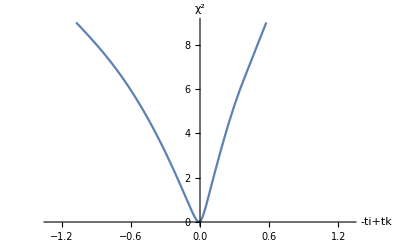

```mathematica
Plot[profilelikelihoodtkminustiinterpolation[x],{x,-1.3,1.3},PlotRange->{0,9},AxesLabel->{tk-ti,χ^2}]
```

```mathematica
NMinimize[{profilelikelihoodtkminustiinterpolation[x], -0.1<=x<=0.1},{x}]
```

{0.00790636,{x→-0.00651224}}

```mathematica
sigmaplustkminusti=Abs[(x/.FindRoot[profilelikelihoodtkminustiinterpolation[x]==1,{x,0.1}])+0.0065122382396871166]
```

0.0729599

```mathematica
sigmaminustkminusti=Abs[(x/.FindRoot[profilelikelihoodtkminustiinterpolation[x]==1,{x,-0.1}])+0.0065122382396871166]
```

0.107064

```mathematica
tbminustitable=Table[{x,-2+0.04x},{x,0,100}]
```

{{0,-2.},{1,-1.96},{2,-1.92},{3,-1.88},{4,-1.84},{5,-1.8},{6,-1.76},{7,-1.72},{8,-1.68},{9,-1.64},{10,-1.6},{11,-1.56},{12,-1.52},{13,-1.48},{14,-1.44},{15,-1.4},{16,-1.36},{17,-1.32},{18,-1.28},{19,-1.24},{20,-1.2},{21,-1.16},{22,-1.12},{23,-1.08},{24,-1.04},{25,-1.},{26,-0.96},{27,-0.92},{28,-0.88},{29,-0.84},{30,-0.8},{31,-0.76},{32,-0.72},{33,-0.68},{34,-0.64},{35,-0.6},{36,-0.56},{37,-0.52},{38,-0.48},{39,-0.44},{40,-0.4},{41,-0.36},{42,-0.32},{43,-0.28},{44,-0.24},{45,-0.2},{46,-0.16},{47,-0.12},{48,-0.08},{49,-0.04},{50,0.},{51,0.04},{52,0.08},{53,0.12},{54,0.16},{55,0.2},{56,0.24},{57,0.28},{58,0.32},{59,0.36},{60,0.4},{61,0.44},{62,0.48},{63,0.52},{64,0.56},{65,0.6},{66,0.64},{67,0.68},{68,0.72},{69,0.76},{70,0.8},{71,0.84},{72,0.88},{73,0.92},{74,0.96},{75,1.},{76,1.04},{77,1.08},{78,1.12},{79,1.16},{80,1.2},{81,1.24},{82,1.28},{83,1.32},{84,1.36},{85,1.4},{86,1.44},{87,1.48},{88,1.52},{89,1.56},{90,1.6},{91,1.64},{92,1.68},{93,1.72},{94,1.76},{95,1.8},{96,1.84},{97,1.88},{98,1.92},{99,1.96},{100,2.}}

```mathematica
profilelikelihoodtbminustiarray=Array[0,101];
```

```mathematica
For[i=0, i<=100,i++,
profilelikelihoodtbminusti[R_, ζ_,T0_,a_,f_,tk_,ti_]:=loglikelihoodtbminusti[R, ζ,T0,a,f,0.1,tk,ti,tbminustitable[[i+1]][[2]]];
If[tbminustitable[[i+1]][[2]]<=0,resulttbminusti=NMinimize[{profilelikelihoodtbminusti[R,ζ,T0,a,f,tk,ti],1*10^6<=R<=3*10^6,0.<=ζ<=0.05,2<=T0<=6,0.1<=a<=1,3<=f<=7,0.0001<=tk<=2,-tbminustitable[[i+1]][[2]]<=ti<=2-tbminustitable[[i+1]][[2]]},{ R,ζ,T0,a,f,tk,ti},MaxIterations->1500],resulttbminusti=NMinimize[{profilelikelihoodtbminusti[R,ζ,T0,a,f,tk,ti],1*10^6<=R<=3*10^6,0.<=ζ<=0.05,2<=T0<=6,0.1<=a<=1,3<=f<=7,0.0001<=tk<=2,0.0001<=ti<=2+0.0001-tbminustitable[[i+1]][[2]]},{ R,ζ,T0,a,f,tk,ti},MaxIterations->1500]];
profilelikelihoodtbminustiarray[[i+1]]=resulttbminusti[[1]];]
```

```mathematica
profilelikelihoodtbminustitable=Table[{tbminustitable[[x+1]][[2]],profilelikelihoodtbminustiarray[[x+1]]-result[[1]]}, {x,0, 100, 1}]
```

{{-2.,13.7542},{-1.96,13.561},{-1.92,13.3679},{-1.88,13.1748},{-1.84,12.9819},{-1.8,12.789},{-1.76,12.5954},{-1.72,12.4007},{-1.68,12.205},{-1.64,12.0082},{-1.6,11.8103},{-1.56,11.6114},{-1.52,11.4114},{-1.48,11.2102},{-1.44,11.0079},{-1.4,10.8044},{-1.36,10.5997},{-1.32,10.3938},{-1.28,10.1865},{-1.24,9.97775},{-1.2,9.76747},{-1.16,9.55546},{-1.12,9.34148},{-1.08,9.1252},{-1.04,8.9062},{-1.,8.6839},{-0.96,8.45759},{-0.92,8.22638},{-0.88,7.98921},{-0.84,7.74485},{-0.8,7.49204},{-0.76,7.22949},{-0.72,6.95607},{-0.68,6.67083},{-0.64,6.37303},{-0.6,6.06215},{-0.56,5.73778},{-0.52,5.39956},{-0.48,5.04718},{-0.44,4.68029},{-0.4,4.29854},{-0.36,3.90144},{-0.32,3.48902},{-0.28,3.06138},{-0.24,2.61904},{-0.2,2.16309},{-0.16,1.69556},{-0.12,1.22031},{-0.08,0.746361},{-0.04,0.303024},{0.,0.0162974},{0.04,0.0774314},{0.08,0.320178},{0.12,0.616817},{0.16,0.935349},{0.2,1.26492},{0.24,1.60007},{0.28,1.9373},{0.32,2.27403},{0.36,2.60826},{0.4,2.9384},{0.44,3.26316},{0.48,3.58151},{0.52,3.89265},{0.56,4.19596},{0.6,4.49096},{0.64,4.77733},{0.68,5.05485},{0.72,5.32337},{0.76,5.58277},{0.8,5.81592},{0.84,6.04091},{0.88,6.26399},{0.92,6.48439},{0.96,6.74677},{1.,6.92636},{1.04,7.07636},{1.08,7.20048},{1.12,7.30648},{1.16,7.40098},{1.2,7.48821},{1.24,7.57073},{1.28,7.65011},{1.32,7.72736},{1.36,7.80311},{1.4,7.8778},{1.44,7.9517},{1.48,8.02501},{1.52,8.09786},{1.56,8.17032},{1.6,8.24245},{1.64,8.3143},{1.68,8.38589},{1.72,8.45724},{1.76,8.52834},{1.8,8.59922},{1.84,8.66988},{1.88,8.74031},{1.92,8.81053},{1.96,8.88231},{2.,20.9496}}

```mathematica
profilelikelihoodtbminustiinterpolation=Interpolation[profilelikelihoodtbminustitable];
```

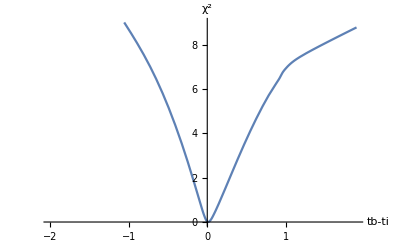

```mathematica
Plot[profilelikelihoodtbminustiinterpolation[x],{x,-2,1.90},PlotRange->{0,9},AxesLabel->{tb-ti,χ^2}]
```

```mathematica
NMinimize[{profilelikelihoodtbminustiinterpolation[x], -0.1<=x<=0.1},{x}]
```

{0.00544508,{x→0.0104346}}

```mathematica
sigmaplustbminusti=Abs[(x/.FindRoot[profilelikelihoodtbminustiinterpolation[x]==1,{x,0.1}])-0.010434634685130433]
```

0.157498

```mathematica
sigmaminustbminusti=Abs[(x/.FindRoot[profilelikelihoodtbminustiinterpolation[x]==1,{x,-0.1}])-0.010434634685130433]
```

0.112004

## Likelihood of the absolute times (point-like earth)

```mathematica
(*T0I is the absolute time of arrival of the first neutrino in IMB (corresponding to 0 time in the flux)*)
(*T1I is the absolute time of detection of the first neutrino*)
(*T1I=T0I+ti, where ti is the delay time for IMB*)
```

```mathematica
(*likelihood T1I*)
```

```mathematica
averageT1I=0.374 (*in s*)
sigmaT1I=0.050 (*in s*)
```

```mathematica
likelihoodT1I[T1I_]:=1/((2Pi)^(1/2)*sigmaT1I)*Exp[-(T1I-averageT1I)^2/(2*(sigmaT1I)^2)];
```

```mathematica
(*likelihood ti*)
```

```mathematica
profileloglikelihoodtiinterpolation=Interpolation[profileloglikelihoodtitable]
```

InterpolatingFunction[…]

```mathematica
chisquareti[ti_]:=profileloglikelihoodtiinterpolation[ti];
```

```mathematica
normalizationlikelihoodti=NIntegrate[Exp[(-chisquareti[ti])/2],{ti,0.0001,1.5}]
```

0.229578

```mathematica
likelihoodti[ti_]:=1/normalizationlikelihoodti Exp[(-chisquareti[ti])/2];
```

```mathematica
(*likelihood and χ^2 of T0I*)
```

```mathematica
likelihoodT1Iti[T1I_,ti_]:=likelihoodT1I[T1I]*likelihoodti[ti];
```

```mathematica
likelihoodT0[T0I_]:=NIntegrate[likelihoodT1Iti[T0I+ti,ti],{ti,0.0001,1.5}];
```

```mathematica
likelihoodT0table=Table[{T0I,likelihoodT0[T0I]},{T0I,-2,1,0.01}]
```

{{-2.,1.77112×10^-70},{-1.99,5.79237×10^-69},{-1.98,1.82033×10^-67},{-1.97,5.4971×10^-66},{-1.96,1.59516×10^-64},{-1.95,4.44801×10^-63},{-1.94,1.19184×10^-61},{-1.93,3.06878×10^-60},{-1.92,7.59288×10^-59},{-1.91,1.80528×10^-57},{-1.9,4.12459×10^-56},{-1.89,9.0556×10^-55},{-1.88,1.91054×10^-53},{-1.87,3.87345×10^-52},{-1.86,7.54651×10^-51},{-1.85,1.41287×10^-49},{-1.84,2.54196×10^-48},{-1.83,4.39489×10^-47},{-1.82,7.30199×10^-46},{-1.81,1.16588×10^-44},{-1.8,1.78889×10^-43},{-1.79,2.63777×10^-42},{-1.78,3.73779×10^-41},{-1.77,5.09005×10^-40},{-1.76,6.66132×10^-39},{-1.75,8.37785×10^-38},{-1.74,1.01261×10^-36},{-1.73,1.17624×10^-35},{-1.72,1.31308×10^-34},{-1.71,1.40876×10^-33},{-1.7,1.45257×10^-32},{-1.69,1.43943×10^-31},{-1.68,1.37091×10^-30},{-1.67,1.25485×10^-29},{-1.66,1.10394×10^-28},{-1.65,9.33421×10^-28},{-1.64,7.58561×10^-27},{-1.63,5.92504×10^-26},{-1.62,4.44821×10^-25},{-1.61,3.20982×10^-24},{-1.6,2.22629×10^-23},{-1.59,1.48422×10^-22},{-1.58,9.51122×10^-22},{-1.57,5.85875×10^-21},{-1.56,3.46906×10^-20},{-1.55,1.97455×10^-19},{-1.54,1.08039×10^-18},{-1.53,5.68282×10^-18},{-1.52,2.8736×10^-17},{-1.51,1.39695×10^-16},{-1.5,6.52888×10^-16},{-1.49,2.9337×10^-15},{-1.48,1.26744×10^-14},{-1.47,5.26486×10^-14},{-1.46,2.10288×10^-13},{-1.45,8.07655×10^-13},{-1.44,2.98293×10^-12},{-1.43,1.05947×10^-11},{-1.42,3.61896×10^-11},{-1.41,1.18893×10^-10},{-1.4,3.75692×10^-10},{-1.39,1.14194×10^-9},{-1.38,3.33906×10^-9},{-1.37,9.39313×10^-9},{-1.36,2.54239×10^-8},{-1.35,6.62162×10^-8},{-1.34,1.65969×10^-7},{-1.33,4.00389×10^-7},{-1.32,9.29805×10^-7},{-1.31,2.07885×10^-6},{-1.3,4.47561×10^-6},{-1.29,9.28028×10^-6},{-1.28,0.0000185373},{-1.27,0.0000356789},{-1.26,0.0000661878},{-1.25,0.000118381},{-1.24,0.000204209},{-1.23,0.000339888},{-1.22,0.000546086},{-1.21,0.000847384},{-1.2,0.00127073},{-1.19,0.00184282},{-1.18,0.00258647},{-1.17,0.00351659},{-1.16,0.00463635},{-1.15,0.0059345},{-1.14,0.00738462},{-1.13,0.00894679},{-1.12,0.0105715},{-1.11,0.0122055},{-1.1,0.013798},{-1.09,0.0153062},{-1.08,0.0166998},{-1.07,0.0179629},{-1.06,0.0190931},{-1.05,0.0200995},{-1.04,0.0209992},{-1.03,0.0218135},{-1.02,0.0225647},{-1.01,0.0232734},{-1.,0.0239572},{-0.99,0.0246301},{-0.98,0.0253026},{-0.97,0.0259821},{-0.96,0.0266738},{-0.95,0.0273811},{-0.94,0.0281061},{-0.93,0.0288507},{-0.92,0.0296158},{-0.91,0.0304024},{-0.9,0.0312114},{-0.89,0.0320434},{-0.88,0.0328994},{-0.87,0.0337801},{-0.86,0.0346863},{-0.85,0.0356188},{-0.84,0.0365786},{-0.83,0.0375667},{-0.82,0.0385838},{-0.81,0.0396312},{-0.8,0.0407098},{-0.79,0.0418208},{-0.78,0.0429653},{-0.77,0.0441446},{-0.76,0.0453599},{-0.75,0.0466128},{-0.74,0.0479044},{-0.73,0.0492365},{-0.72,0.0506106},{-0.71,0.0520284},{-0.7,0.0534917},{-0.69,0.0550023},{-0.68,0.0565624},{-0.67,0.0581739},{-0.66,0.0598392},{-0.65,0.0615606},{-0.64,0.0633406},{-0.63,0.065182},{-0.62,0.0670876},{-0.61,0.0690605},{-0.6,0.0711038},{-0.59,0.073221},{-0.58,0.0754157},{-0.57,0.0776917},{-0.56,0.0800533},{-0.55,0.0825048},{-0.54,0.0850507},{-0.53,0.0876961},{-0.52,0.0904461},{-0.51,0.0933064},{-0.5,0.0962828},{-0.49,0.0993816},{-0.48,0.102609},{-0.47,0.105973},{-0.46,0.109481},{-0.45,0.11314},{-0.44,0.116959},{-0.43,0.120947},{-0.42,0.125113},{-0.41,0.129467},{-0.4,0.13402},{-0.39,0.138783},{-0.38,0.143769},{-0.37,0.148989},{-0.36,0.154457},{-0.35,0.160187},{-0.34,0.166195},{-0.33,0.172497},{-0.32,0.179109},{-0.31,0.186049},{-0.3,0.193338},{-0.29,0.200995},{-0.28,0.209041},{-0.27,0.217502},{-0.26,0.2264},{-0.25,0.235762},{-0.24,0.245616},{-0.23,0.255993},{-0.22,0.266924},{-0.21,0.278444},{-0.2,0.290588},{-0.19,0.303396},{-0.18,0.316909},{-0.17,0.331173},{-0.16,0.346234},{-0.15,0.362145},{-0.14,0.378959},{-0.13,0.396736},{-0.12,0.415539},{-0.11,0.435435},{-0.1,0.456497},{-0.09,0.478803},{-0.08,0.502436},{-0.07,0.527485},{-0.06,0.554047},{-0.05,0.582224},{-0.04,0.612126},{-0.03,0.643873},{-0.02,0.677589},{-0.01,0.713412},{0.,0.751487},{0.01,0.79197},{0.02,0.835027},{0.03,0.880837},{0.04,0.92959},{0.05,0.98149},{0.06,1.03675},{0.07,1.09561},{0.08,1.15831},{0.09,1.2251},{0.1,1.29626},{0.11,1.37208},{0.12,1.45285},{0.13,1.53886},{0.14,1.63041},{0.15,1.7278},{0.16,1.83126},{0.17,1.94099},{0.18,2.05704},{0.19,2.17931},{0.2,2.30738},{0.21,2.44039},{0.22,2.57687},{0.23,2.7145},{0.24,2.84991},{0.25,2.97844},{0.26,3.09409},{0.27,3.18957},{0.28,3.25663},{0.29,3.28669},{0.3,3.27171},{0.31,3.20536},{0.32,3.08415},{0.33,2.90836},{0.34,2.68264},{0.35,2.41595},{0.36,2.12077},{0.37,1.81185},{0.38,1.50445},{0.39,1.21265},{0.4,0.947809},{0.41,0.71767},{0.42,0.525992},{0.43,0.372875},{0.44,0.255502},{0.45,0.169132},{0.46,0.108102},{0.47,0.0666856},{0.48,0.0396869},{0.49,0.0227787},{0.5,0.0126051},{0.51,0.00672328},{0.52,0.00345563},{0.53,0.00171117},{0.54,0.000816197},{0.55,0.000374937},{0.56,0.00016585},{0.57,0.0000706331},{0.58,0.0000289589},{0.59,0.0000114285},{0.6,4.34092×10^-6},{0.61,1.5868×10^-6},{0.62,5.58184×10^-7},{0.63,1.88934×10^-7},{0.64,6.15305×10^-8},{0.65,1.92793×10^-8},{0.66,5.81152×10^-9},{0.67,1.68523×10^-9},{0.68,4.70091×10^-10},{0.69,1.26135×10^-10},{0.7,3.25538×10^-11},{0.71,8.08099×10^-12},{0.72,1.92934×10^-12},{0.73,4.43017×10^-13},{0.74,9.78329×10^-14},{0.75,2.07774×10^-14},{0.76,4.24351×10^-15},{0.77,8.33447×10^-16},{0.78,1.57412×10^-16},{0.79,2.8589×10^-17},{0.8,4.99283×10^-18},{0.81,8.38449×10^-19},{0.82,1.35388×10^-19},{0.83,2.10207×10^-20},{0.84,3.13815×10^-21},{0.85,4.50454×10^-22},{0.86,6.21689×10^-23},{0.87,8.24962×10^-24},{0.88,1.05251×10^-24},{0.89,1.29107×10^-25},{0.9,1.52262×10^-26},{0.91,1.72644×10^-27},{0.92,1.88201×10^-28},{0.93,1.97242×10^-29},{0.94,1.98738×10^-30},{0.95,1.92513×10^-31},{0.96,1.7928×10^-32},{0.97,1.60507×10^-33},{0.98,1.38147×10^-34},{0.99,1.14307×10^-35},{1.,9.09243×10^-37}}

```mathematica
likelihoodT0interpolation=Interpolation[likelihoodT0table]
```

InterpolatingFunction[…]

```mathematica
normalizationlikelihoodT0=NIntegrate[likelihoodT0interpolation[x],{x,-2,1}]
```

1.

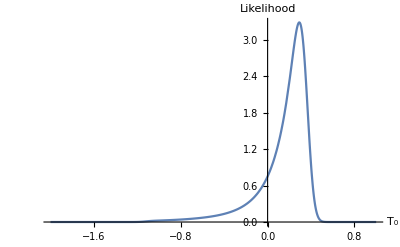

```mathematica
Plot[likelihoodT0interpolation[x],{x,-2,1},PlotRange->All,AxesLabel->{Subscript[T, 0],Likelihood}]
```

```mathematica
NMaximize[{likelihoodT0interpolation[x],0.270<=x<=0.400},{x}]
```

{3.2875,{x→0.291884}}

```mathematica
chisquareT0I[T0I_]:=-2Log[likelihoodT0interpolation[T0I]]+2Log[likelihoodT0interpolation[0.2918837503102832]];
```

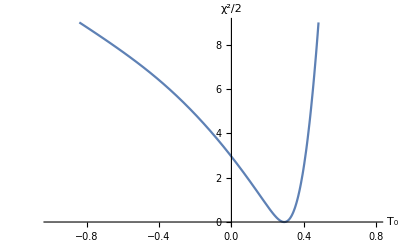

```mathematica
Plot[chisquareT0I[x],{x,-1,0.8},AxesLabel->{Subscript[T, 0],χ^2/2},PlotRange->{0,9}]
```

```mathematica
NMinimize[{chisquareT0I[x],0.2<=x<=0.4},{x}]
```

{0.,{x→0.291884}}

```mathematica
sigmaplusT0I=Abs[(x/.FindRoot[chisquareT0I[x]==1,{x,0.35}])-0.2918837503102832]
```

0.0722465

```mathematica
sigmaminusT0I=Abs[(x/.FindRoot[chisquareT0I[x]==1,{x,0.15}])-0.2918837503102832]
```

0.117251

```mathematica
(*T0KK is the absolute time of arrival of the first neutrino in KK(corresponding to 0 time in the flux). For a point-like Earth T0I=T0KK*)
(*T1KK is the absolute time of detection of the first neutrino in KK*)
(*T1KK=T0KK+tk, where tk is the delay time for IMB*)
```

```mathematica
(*likelihood ti*)
```

```mathematica
profileloglikelihoodtkinterpolation=Interpolation[profileloglikelihoodtktable]
```

InterpolatingFunction[…]

```mathematica
chisquaretk[tk_]:=profileloglikelihoodtkinterpolation[tk];
```

```mathematica
normalizationlikelihoodtk=NIntegrate[Exp[(-chisquaretk[tk])/2],{tk,0.0001,0.8}]
```

0.144248

```mathematica
likelihoodtk[tk_]:=1/normalizationlikelihoodtk Exp[(-chisquaretk[tk])/2];
```

```mathematica
(*likelihood T1KK, assuming that the three time parameters are independent from each other*)
```

```mathematica
likelihoodT1Ititk[T1I_,ti_,tk_]:=likelihoodT1I[T1I]*likelihoodti[ti]*likelihoodtk[tk];
```

```mathematica
likelihoodT1KK[T1KK_]:=NIntegrate[likelihoodT1I[T1KK-tk+ti]*likelihoodti[ti]*likelihoodtk[tk],{tk,0.0001,0.8},{ti,0.0001,1.5}];
```

```mathematica
likelihoodT1KKtable=Table[{x,likelihoodT1KK[x]},{x,-2,2,0.01}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{-2.,2.83431×10^-73},{-1.99,9.56591×10^-72},{-1.98,3.10325×10^-70},{-1.97,9.67655×10^-69},{-1.96,2.90029×10^-67},{-1.95,8.35568×10^-66},{-1.94,2.3139×10^-64},{-1.93,6.15933×10^-63},{-1.92,1.57598×10^-61},{-1.91,3.87616×10^-60},{-1.9,9.16407×10^-59},{-1.89,2.08264×10^-57},{-1.88,4.54972×10^-56},{-1.87,9.55436×10^-55},{-1.86,1.92872×10^-53},{-1.85,3.74277×10^-52},{-1.84,6.98195×10^-51},{-1.83,1.25206×10^-49},{-1.82,2.15844×10^-48},{-1.81,3.57708×10^-47},{-1.8,5.69898×10^-46},{-1.79,8.72867×10^-45},{-1.78,1.28525×10^-43},{-1.77,1.81937×10^-42},{-1.76,2.47603×10^-41},{-1.75,3.23965×10^-40},{-1.74,4.07522×10^-39},{-1.73,4.92859×10^-38},{-1.72,5.73088×10^-37},{-1.71,6.40697×10^-36},{-1.7,6.88691×10^-35},{-1.69,7.11778×10^-34},{-1.68,7.07328×10^-33},{-1.67,6.7587×10^-32},{-1.66,6.20982×10^-31},{-1.65,5.48629×10^-30},{-1.64,4.66093×10^-29},{-1.63,3.80776×10^-28},{-1.62,2.99145×10^-27},{-1.61,2.26007×10^-26},{-1.6,1.6421×10^-25},{-1.59,1.14744×10^-24},{-1.58,7.71128×10^-24},{-1.57,4.98428×10^-23},{-1.56,3.09866×10^-22},{-1.55,1.85292×10^-21},{-1.54,1.06578×10^-20},{-1.53,5.89694×10^-20},{-1.52,3.13871×10^-19},{-1.51,1.60717×10^-18},{-1.5,7.91741×10^-18},{-1.49,3.75263×10^-17},{-1.48,1.71138×10^-16},{-1.47,7.51×10^-16},{-1.46,3.17137×10^-15},{-1.45,1.28883×10^-14},{-1.44,5.04105×10^-14},{-1.43,1.89783×10^-13},{-1.42,6.87768×10^-13},{-1.41,2.39948×10^-12},{-1.4,8.0598×10^-12},{-1.39,2.60683×10^-11},{-1.38,8.11956×10^-11},{-1.37,2.43579×10^-10},{-1.36,7.03872×10^-10},{-1.35,1.95956×10^-9},{-1.34,5.25664×10^-9},{-1.33,1.35899×10^-8},{-1.32,3.38662×10^-8},{-1.31,8.13676×10^-8},{-1.3,1.88526×10^-7},{-1.29,4.21339×10^-7},{-1.28,9.08565×10^-7},{-1.27,1.89092×10^-6},{-1.26,3.7995×10^-6},{-1.25,7.37351×10^-6},{-1.24,0.0000138258},{-1.23,0.0000250591},{-1.22,0.0000439246},{-1.21,0.0000744993},{-1.2,0.000122335},{-1.19,0.000194619},{-1.18,0.000300166},{-1.17,0.000449179},{-1.16,0.000652723},{-1.15,0.000921924},{-1.14,0.00126695},{-1.13,0.00169588},{-1.12,0.0022137},{-1.11,0.00282151},{-1.1,0.00351614},{-1.09,0.00429032},{-1.08,0.00513324},{-1.07,0.00603158},{-1.06,0.00697071},{-1.05,0.00793596},{-1.04,0.00891373},{-1.03,0.00989229},{-1.02,0.0108623},{-1.01,0.011817},{-1.,0.0127521},{-0.99,0.0136653},{-0.98,0.0145563},{-0.97,0.0154258},{-0.96,0.0162758},{-0.95,0.0171085},{-0.94,0.0179266},{-0.93,0.018733},{-0.92,0.0195304},{-0.91,0.0203216},{-0.9,0.0211091},{-0.89,0.0218954},{-0.88,0.0226828},{-0.87,0.0234733},{-0.86,0.024269},{-0.85,0.0250718},{-0.84,0.0258835},{-0.83,0.0267056},{-0.82,0.0275398},{-0.81,0.0283876},{-0.8,0.0292504},{-0.79,0.0301296},{-0.78,0.0310266},{-0.77,0.0319426},{-0.76,0.0328791},{-0.75,0.0338373},{-0.74,0.0348184},{-0.73,0.0358238},{-0.72,0.0368547},{-0.71,0.0379124},{-0.7,0.0389983},{-0.69,0.0401136},{-0.68,0.0412598},{-0.67,0.0424384},{-0.66,0.0436506},{-0.65,0.0448981},{-0.64,0.0461825},{-0.63,0.0475053},{-0.62,0.0488684},{-0.61,0.0502736},{-0.6,0.0517227},{-0.59,0.0532178},{-0.58,0.0547611},{-0.57,0.0563546},{-0.56,0.0580009},{-0.55,0.0597023},{-0.54,0.0614615},{-0.53,0.0632814},{-0.52,0.0651649},{-0.51,0.0671151},{-0.5,0.0691353},{-0.49,0.0712291},{-0.48,0.0734001},{-0.47,0.0756524},{-0.46,0.07799},{-0.45,0.0804176},{-0.44,0.0829396},{-0.43,0.0855612},{-0.42,0.0882876},{-0.41,0.0911245},{-0.4,0.0940776},{-0.39,0.0971534},{-0.38,0.100358},{-0.37,0.1037},{-0.36,0.107185},{-0.35,0.110822},{-0.34,0.114619},{-0.33,0.118585},{-0.32,0.122729},{-0.31,0.127063},{-0.3,0.131595},{-0.29,0.136338},{-0.28,0.141304},{-0.27,0.146506},{-0.26,0.151956},{-0.25,0.157671},{-0.24,0.163664},{-0.23,0.169952},{-0.22,0.176553},{-0.21,0.183485},{-0.2,0.190768},{-0.19,0.198422},{-0.18,0.20647},{-0.17,0.214936},{-0.16,0.223844},{-0.15,0.233223},{-0.14,0.2431},{-0.13,0.253507},{-0.12,0.264476},{-0.11,0.276044},{-0.1,0.288246},{-0.09,0.301125},{-0.08,0.314723},{-0.07,0.329085},{-0.06,0.344263},{-0.05,0.360308},{-0.04,0.377278},{-0.03,0.395234},{-0.02,0.41424},{-0.01,0.434367},{0.,0.455689},{0.01,0.478287},{0.02,0.502248},{0.03,0.527662},{0.04,0.554629},{0.05,0.583255},{0.06,0.613653},{0.07,0.645944},{0.08,0.680258},{0.09,0.716733},{0.1,0.755516},{0.11,0.796767},{0.12,0.84065},{0.13,0.887344},{0.14,0.937037},{0.15,0.989924},{0.16,1.04621},{0.17,1.10611},{0.18,1.16983},{0.19,1.23757},{0.2,1.30953},{0.21,1.38587},{0.22,1.46667},{0.23,1.55193},{0.24,1.64152},{0.25,1.73506},{0.26,1.83192},{0.27,1.93109},{0.28,2.0311},{0.29,2.12999},{0.3,2.22526},{0.31,2.3139},{0.32,2.39256},{0.33,2.45767},{0.34,2.50576},{0.35,2.53375},{0.36,2.5393},{0.37,2.52106},{0.38,2.47886},{0.39,2.41378},{0.4,2.32809},{0.41,2.22498},{0.42,2.10831},{0.43,1.98224},{0.44,1.85087},{0.45,1.71798},{0.46,1.58678},{0.47,1.45986},{0.48,1.3391},{0.49,1.22571},{0.5,1.12039},{0.51,1.02336},{0.52,0.934535},{0.53,0.853578},{0.54,0.780027},{0.55,0.713339},{0.56,0.652945},{0.57,0.598279},{0.58,0.548802},{0.59,0.504006},{0.6,0.463427},{0.61,0.426639},{0.62,0.393258},{0.63,0.362936},{0.64,0.335362},{0.65,0.310255},{0.66,0.287364},{0.67,0.266463},{0.68,0.247351},{0.69,0.229847},{0.7,0.213788},{0.71,0.199029},{0.72,0.18544},{0.73,0.172905},{0.74,0.161321},{0.75,0.150595},{0.76,0.140647},{0.77,0.131404},{0.78,0.122802},{0.79,0.114785},{0.8,0.107303},{0.81,0.100314},{0.82,0.093778},{0.83,0.0876612},{0.84,0.0819326},{0.85,0.0765647},{0.86,0.071532},{0.87,0.0668115},{0.88,0.0623817},{0.89,0.0582226},{0.9,0.0543157},{0.91,0.0506433},{0.92,0.0471892},{0.93,0.0439377},{0.94,0.0408742},{0.95,0.0379849},{0.96,0.0352567},{0.97,0.0326772},{0.98,0.0302351},{0.99,0.0279192},{1.,0.0257197},{1.01,0.0236272},{1.02,0.0216332},{1.03,0.0197305},{1.04,0.0179126},{1.05,0.0161749},{1.06,0.0145139},{1.07,0.0129283},{1.08,0.0114185},{1.09,0.00998699},{1.1,0.00863819},{1.11,0.007378},{1.12,0.00621326},{1.13,0.0051509},{1.14,0.00419704},{1.15,0.00335595},{1.16,0.00262924},{1.17,0.0020153},{1.18,0.00150914},{1.19,0.00110259},{1.2,0.000784961},{1.21,0.00054391},{1.22,0.000366424},{1.23,0.000239768},{1.24,0.000152251},{1.25,0.0000937418},{1.26,0.000055923},{1.27,0.0000323028},{1.28,0.0000180559},{1.29,9.7609×10^-6},{1.3,5.10078×10^-6},{1.31,2.57552×10^-6},{1.32,1.25603×10^-6},{1.33,5.91402×10^-7},{1.34,2.68763×10^-7},{1.35,1.1785×10^-7},{1.36,4.98476×10^-8},{1.37,2.03333×10^-8},{1.38,7.99688×10^-9},{1.39,3.03176×10^-9},{1.4,1.10776×10^-9},{1.41,3.90036×10^-10},{1.42,1.32312×10^-10},{1.43,4.32383×10^-11},{1.44,1.36099×10^-11},{1.45,4.12575×10^-12},{1.46,1.20439×10^-12},{1.47,3.38533×10^-13},{1.48,9.16144×10^-14},{1.49,2.3868×10^-14},{1.5,5.9858×10^-15},{1.51,1.44494×10^-15},{1.52,3.35711×10^-16},{1.53,7.50661×10^-17},{1.54,1.61531×10^-17},{1.55,3.34485×10^-18},{1.56,6.66475×10^-19},{1.57,1.27777×10^-19},{1.58,2.35704×10^-20},{1.59,4.18316×10^-21},{1.6,7.14244×10^-22},{1.61,1.17321×10^-22},{1.62,1.85387×10^-23},{1.63,2.81797×10^-24},{1.64,4.12037×10^-25},{1.65,5.79515×10^-26},{1.66,7.84027×10^-27},{1.67,1.02013×10^-27},{1.68,1.27671×10^-28},{1.69,1.53677×10^-29},{1.7,1.77907×10^-30},{1.71,1.98079×10^-31},{1.72,2.12096×10^-32},{1.73,2.18406×10^-33},{1.74,2.16287×10^-34},{1.75,2.05976×10^-35},{1.76,1.88633×10^-36},{1.77,1.66121×10^-37},{1.78,1.40679×10^-38},{1.79,1.14559×10^-39},{1.8,8.97034×10^-41},{1.81,6.75411×10^-42},{1.82,4.88988×10^-43},{1.83,3.40403×10^-44},{1.84,2.27849×10^-45},{1.85,1.4664×10^-46},{1.86,9.07416×10^-48},{1.87,5.39885×10^-49},{1.88,3.08839×10^-50},{1.89,1.69861×10^-51},{1.9,8.98215×10^-53},{1.91,4.56655×10^-54},{1.92,2.23209×10^-55},{1.93,1.04893×10^-56},{1.94,4.73902×10^-58},{1.95,2.05841×10^-59},{1.96,8.59554×10^-61},{1.97,3.45071×10^-62},{1.98,1.33178×10^-63},{1.99,4.94131×10^-65},{2.,1.76252×10^-66}}

```mathematica
likelihoodT1KKinterpolation=Interpolation[likelihoodT1KKtable]
```

InterpolatingFunction[…]

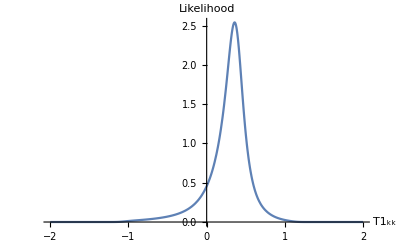

```mathematica
Plot[likelihoodT1KKinterpolation[x],{x,-2,2},PlotRange->All,AxesLabel->{Subscript[T1, kk], Likelihood}]
```

```mathematica
NMaximize[{likelihoodT1KKinterpolation[x],0.270<=x<=0.500},{x}]
```

{2.54009,{x→0.357408}}

```mathematica
chisquareT1KK[T1KK_]:=-2Log[likelihoodT1KKinterpolation[T1KK]]+2Log[likelihoodT1KKinterpolation[0.35740820186422895]];
```

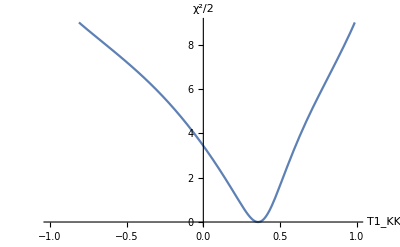

```mathematica
Plot[chisquareT1KK[x],{x,-1,1},AxesLabel->{Subscript[T1, KK],χ^2/2},PlotRange->{0,9}]
```

```mathematica
NMinimize[{chisquareT1KK[x],0.2<=x<=0.4},{x}]
```

{0.,{x→0.357408}}

```mathematica
sigmaplusT1KK=Abs[(x/.FindRoot[chisquareT1KK[x]==1,{x,0.45}])-0.35740820144920543]
```

0.106181

```mathematica
sigmaminusT1KK=Abs[(x/.FindRoot[chisquareT1KK[x]==1,{x,0.20}])-0.35740820144920543]
```

0.128703

```mathematica
(*T0B is the absolute time of arrival of the first neutrino in Baksan(corresponding to 0 time in the flux). For a point-like Earth T0B=T0I*)
(*T1B is the absolute time of detection of the first neutrino in Baksan*)
(*T1B=T0B+tb, where tb is the delay time for IMB*)
```

```mathematica
(*likelihood tb*)
```

```mathematica
profileloglikelihoodtbinterpolation=Interpolation[profileloglikelihoodtbtable]
```

InterpolatingFunction[…]

```mathematica
chisquaretb[tb_]:=profileloglikelihoodtbinterpolation[tb];
```

```mathematica
normalizationlikelihoodtb=NIntegrate[Exp[(-chisquaretb[tb])/2],{tb,0.0001,2.5}]
```

0.331378

```mathematica
likelihoodtb[tb_]:=1/normalizationlikelihoodtb Exp[(-chisquaretb[tb])/2];
```

```mathematica
(*likelihood T1B, assuming that the three time parameters are independent from each other*)
```

```mathematica
likelihoodT1Ititb[T1I_,ti_,tb_]:=likelihoodT1I[T1I]*likelihoodti[ti]*likelihoodtb[tb];
```

```mathematica
likelihoodT1B[T1B_]:=NIntegrate[likelihoodT1Ititb[T1B-tb+ti,ti,tb],{ti,0.0001,1.5},{tb,0.0001,2.5}];
```

```mathematica
likelihoodT1Btable=Table[{x,likelihoodT1B[x]},{x,-2,2.5,0.01}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{-2.,6.08238×10^-74},{-1.99,2.03736×10^-72},{-1.98,6.56019×10^-71},{-1.97,2.03059×10^-69},{-1.96,6.04213×10^-68},{-1.95,1.72834×10^-66},{-1.94,4.75271×10^-65},{-1.93,1.25642×10^-63},{-1.92,3.19314×10^-62},{-1.91,7.80179×10^-61},{-1.9,1.83262×10^-59},{-1.89,4.13864×10^-58},{-1.88,8.98585×10^-57},{-1.87,1.87579×10^-55},{-1.86,3.76477×10^-54},{-1.85,7.26494×10^-53},{-1.84,1.34794×10^-51},{-1.83,2.40474×10^-50},{-1.82,4.12502×10^-49},{-1.81,6.8039×10^-48},{-1.8,1.07912×10^-46},{-1.79,1.6458×10^-45},{-1.78,2.4137×10^-44},{-1.77,3.4041×10^-43},{-1.76,4.61681×10^-42},{-1.75,6.02165×10^-41},{-1.74,7.55323×10^-40},{-1.73,9.11183×10^-39},{-1.72,1.05717×10^-37},{-1.71,1.17968×10^-36},{-1.7,1.26613×10^-35},{-1.69,1.30706×10^-34},{-1.68,1.29787×10^-33},{-1.67,1.23966×10^-32},{-1.66,1.13899×10^-31},{-1.65,1.0067×10^-30},{-1.64,8.55964×10^-30},{-1.63,7.00175×10^-29},{-1.62,5.5102×10^-28},{-1.61,4.1721×10^-27},{-1.6,3.0394×10^-26},{-1.59,2.13051×10^-25},{-1.58,1.43702×10^-24},{-1.57,9.32699×10^-24},{-1.56,5.82563×10^-23},{-1.55,3.50177×10^-22},{-1.54,2.02581×10^-21},{-1.53,1.12797×10^-20},{-1.52,6.04514×10^-20},{-1.51,3.11856×10^-19},{-1.5,1.54869×10^-18},{-1.49,7.40394×10^-18},{-1.48,3.40785×10^-17},{-1.47,1.51024×10^-16},{-1.46,6.4445×10^-16},{-1.45,2.64816×10^-15},{-1.44,1.04796×10^-14},{-1.43,3.99419×10^-14},{-1.42,1.46634×10^-13},{-1.41,5.1856×10^-13},{-1.4,1.76673×10^-12},{-1.39,5.7995×10^-12},{-1.38,1.83447×10^-11},{-1.37,5.59221×10^-11},{-1.36,1.6431×10^-10},{-1.35,4.65386×10^-10},{-1.34,1.27086×10^-9},{-1.33,3.34645×10^-9},{-1.32,8.49869×10^-9},{-1.31,2.08201×10^-8},{-1.3,4.92115×10^-8},{-1.29,1.12254×10^-7},{-1.28,2.4717×10^-7},{-1.27,5.25492×10^-7},{-1.26,1.07905×10^-6},{-1.25,2.14077×10^-6},{-1.24,4.1049×10^-6},{-1.23,7.61054×10^-6},{-1.22,0.000013649},{-1.21,0.0000236903},{-1.2,0.0000398164},{-1.19,0.0000648388},{-1.18,0.000102371},{-1.17,0.000156822},{-1.16,0.000233281},{-1.15,0.000337269},{-1.14,0.000474378},{-1.13,0.000649806},{-1.12,0.00086787},{-1.11,0.00113155},{-1.1,0.00144218},{-1.09,0.00179927},{-1.08,0.00220056},{-1.07,0.00264233},{-1.06,0.00311973},{-1.05,0.00362731},{-1.04,0.00415952},{-1.03,0.00471106},{-1.02,0.00527727},{-1.01,0.00585424},{-1.,0.00643892},{-0.99,0.00702904},{-0.98,0.00762304},{-0.97,0.00821996},{-0.96,0.00881927},{-0.95,0.00942078},{-0.94,0.0100245},{-0.93,0.0106308},{-0.92,0.0112399},{-0.91,0.0118523},{-0.9,0.0124684},{-0.89,0.0130888},{-0.88,0.013714},{-0.87,0.0143447},{-0.86,0.0149814},{-0.85,0.0156249},{-0.84,0.0162756},{-0.83,0.0169342},{-0.82,0.0176016},{-0.81,0.0182782},{-0.8,0.0189648},{-0.79,0.0196622},{-0.78,0.020371},{-0.77,0.021092},{-0.76,0.0218259},{-0.75,0.0225735},{-0.74,0.0233355},{-0.73,0.0241129},{-0.72,0.0249063},{-0.71,0.0257167},{-0.7,0.026545},{-0.69,0.0273919},{-0.68,0.0282585},{-0.67,0.0291457},{-0.66,0.0300545},{-0.65,0.030986},{-0.64,0.0319411},{-0.63,0.032921},{-0.62,0.0339269},{-0.61,0.03496},{-0.6,0.0360215},{-0.59,0.0371127},{-0.58,0.0382351},{-0.57,0.0393901},{-0.56,0.0405792},{-0.55,0.041804},{-0.54,0.0430661},{-0.53,0.0443675},{-0.52,0.0457098},{-0.51,0.0470952},{-0.5,0.0485256},{-0.49,0.0500034},{-0.48,0.0515307},{-0.47,0.05311},{-0.46,0.054744},{-0.45,0.0564354},{-0.44,0.0581871},{-0.43,0.0600021},{-0.42,0.0618838},{-0.41,0.0638355},{-0.4,0.0658609},{-0.39,0.0679638},{-0.38,0.0701484},{-0.37,0.0724189},{-0.36,0.0747801},{-0.35,0.0772366},{-0.34,0.0797935},{-0.33,0.0824568},{-0.32,0.0852317},{-0.31,0.0881245},{-0.3,0.0911417},{-0.29,0.0942903},{-0.28,0.0975775},{-0.27,0.101011},{-0.26,0.104599},{-0.25,0.10835},{-0.24,0.112274},{-0.23,0.11638},{-0.22,0.12068},{-0.21,0.125182},{-0.2,0.129901},{-0.19,0.134848},{-0.18,0.140036},{-0.17,0.145481},{-0.16,0.151196},{-0.15,0.157198},{-0.14,0.163505},{-0.13,0.170135},{-0.12,0.177106},{-0.11,0.184441},{-0.1,0.192162},{-0.09,0.200292},{-0.08,0.208857},{-0.07,0.217884},{-0.06,0.227402},{-0.05,0.237443},{-0.04,0.248039},{-0.03,0.259228},{-0.02,0.271046},{-0.01,0.283535},{0.,0.296738},{0.01,0.310703},{0.02,0.325479},{0.03,0.341121},{0.04,0.357687},{0.05,0.375237},{0.06,0.393838},{0.07,0.413561},{0.08,0.434481},{0.09,0.456679},{0.1,0.480242},{0.11,0.505263},{0.12,0.531838},{0.13,0.560074},{0.14,0.590081},{0.15,0.621977},{0.16,0.655886},{0.17,0.691938},{0.18,0.730267},{0.19,0.771009},{0.2,0.8143},{0.21,0.860267},{0.22,0.909023},{0.23,0.96065},{0.24,1.01518},{0.25,1.07259},{0.26,1.13272},{0.27,1.19529},{0.28,1.25985},{0.29,1.32569},{0.3,1.39189},{0.31,1.45724},{0.32,1.52031},{0.33,1.57946},{0.34,1.63297},{0.35,1.67912},{0.36,1.71637},{0.37,1.74346},{0.38,1.75957},{0.39,1.76436},{0.4,1.75804},{0.41,1.74129},{0.42,1.71519},{0.43,1.68114},{0.44,1.64065},{0.45,1.59526},{0.46,1.54642},{0.47,1.49539},{0.48,1.44326},{0.49,1.39087},{0.5,1.33886},{0.51,1.28769},{0.52,1.2377},{0.53,1.18909},{0.54,1.14199},{0.55,1.09647},{0.56,1.05256},{0.57,1.01028},{0.58,0.969605},{0.59,0.930514},{0.6,0.892975},{0.61,0.856947},{0.62,0.822391},{0.63,0.78926},{0.64,0.757509},{0.65,0.727092},{0.66,0.697961},{0.67,0.670069},{0.68,0.64337},{0.69,0.617819},{0.7,0.593369},{0.71,0.569977},{0.72,0.5476},{0.73,0.526197},{0.74,0.505725},{0.75,0.486147},{0.76,0.467424},{0.77,0.449519},{0.78,0.432397},{0.79,0.416023},{0.8,0.400365},{0.81,0.38539},{0.82,0.37107},{0.83,0.357374},{0.84,0.344274},{0.85,0.331744},{0.86,0.319758},{0.87,0.308292},{0.88,0.297322},{0.89,0.286825},{0.9,0.276781},{0.91,0.267169},{0.92,0.257969},{0.93,0.249163},{0.94,0.240734},{0.95,0.232663},{0.96,0.224935},{0.97,0.217535},{0.98,0.210449},{0.99,0.203661},{1.,0.19716},{1.01,0.190932},{1.02,0.184965},{1.03,0.179249},{1.04,0.173772},{1.05,0.168523},{1.06,0.163495},{1.07,0.158675},{1.08,0.154057},{1.09,0.149631},{1.1,0.14539},{1.11,0.141324},{1.12,0.137426},{1.13,0.133689},{1.14,0.130106},{1.15,0.126668},{1.16,0.123369},{1.17,0.120203},{1.18,0.117162},{1.19,0.114242},{1.2,0.111435},{1.21,0.108739},{1.22,0.106147},{1.23,0.103658},{1.24,0.101269},{1.25,0.098976},{1.26,0.0967793},{1.27,0.0946772},{1.28,0.0926687},{1.29,0.0907529},{1.3,0.0889283},{1.31,0.0871935},{1.32,0.0855462},{1.33,0.0839836},{1.34,0.0825025},{1.35,0.0810988},{1.36,0.0797682},{1.37,0.0785062},{1.38,0.0773081},{1.39,0.076169},{1.4,0.0750842},{1.41,0.0740494},{1.42,0.0730604},{1.43,0.0721132},{1.44,0.0712044},{1.45,0.0703306},{1.46,0.0694886},{1.47,0.0686758},{1.48,0.0678897},{1.49,0.0671278},{1.5,0.0663883},{1.51,0.065669},{1.52,0.0649684},{1.53,0.064285},{1.54,0.0636174},{1.55,0.0629643},{1.56,0.0623247},{1.57,0.0616976},{1.58,0.0610821},{1.59,0.0604775},{1.6,0.0598831},{1.61,0.0592984},{1.62,0.0587226},{1.63,0.0581555},{1.64,0.0575964},{1.65,0.0570451},{1.66,0.0565012},{1.67,0.0559643},{1.68,0.0554342},{1.69,0.0549106},{1.7,0.0543933},{1.71,0.053882},{1.72,0.0533766},{1.73,0.0528767},{1.74,0.0523824},{1.75,0.0518934},{1.76,0.0514095},{1.77,0.0509307},{1.78,0.0504568},{1.79,0.0499877},{1.8,0.0495232},{1.81,0.0490633},{1.82,0.0486078},{1.83,0.0481567},{1.84,0.0477099},{1.85,0.0472672},{1.86,0.0468287},{1.87,0.0463941},{1.88,0.0459635},{1.89,0.0455367},{1.9,0.0451138},{1.91,0.0446945},{1.92,0.0442789},{1.93,0.0438668},{1.94,0.0434583},{1.95,0.0430532},{1.96,0.0426515},{1.97,0.042253},{1.98,0.0418578},{1.99,0.0414658},{2.,0.0410769},{2.01,0.040691},{2.02,0.0403081},{2.03,0.0399281},{2.04,0.0395509},{2.05,0.0391766},{2.06,0.0388049},{2.07,0.0384359},{2.08,0.0380694},{2.09,0.0377054},{2.1,0.0373439},{2.11,0.0369847},{2.12,0.0366277},{2.13,0.036273},{2.14,0.0359203},{2.15,0.0355697},{2.16,0.035221},{2.17,0.0348742},{2.18,0.0345291},{2.19,0.0341857},{2.2,0.0338439},{2.21,0.0335035},{2.22,0.0331645},{2.23,0.0328267},{2.24,0.0324901},{2.25,0.0321545},{2.26,0.0318197},{2.27,0.0314858},{2.28,0.0311524},{2.29,0.0308195},{2.3,0.030487},{2.31,0.0301546},{2.32,0.0298223},{2.33,0.0294898},{2.34,0.0291569},{2.35,0.0288235},{2.36,0.0284894},{2.37,0.0281543},{2.38,0.027818},{2.39,0.0274803},{2.4,0.0271409},{2.41,0.0267996},{2.42,0.026456},{2.43,0.02611},{2.44,0.025761},{2.45,0.0254089},{2.46,0.0250532},{2.47,0.0246935},{2.48,0.0243295},{2.49,0.0239607},{2.5,0.0235866}}

```mathematica
likelihoodT1Binterpolation=Interpolation[likelihoodT1Btable]
```

InterpolatingFunction[…]

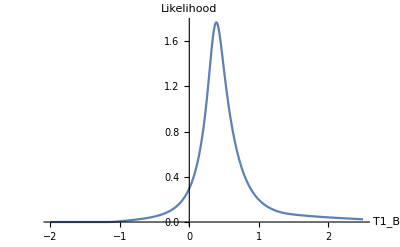

```mathematica
Plot[likelihoodT1Binterpolation[x],{x,-2,2.5},PlotRange->All,AxesLabel->{Subscript[T1, B], Likelihood}]
```

```mathematica
NMaximize[{likelihoodT1Binterpolation[x],0.1<=x<=0.400},{x}]
```

{1.76439,{x→0.389282}}

```mathematica
chisquareT1B[T1B_]:=-2Log[likelihoodT1Binterpolation[T1B]]+2Log[likelihoodT1Binterpolation[0.3892821326220788]];
```

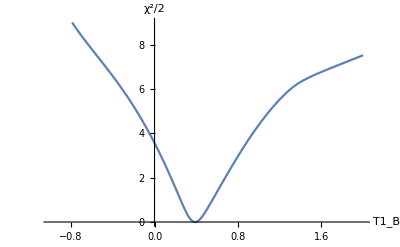

```mathematica
Plot[chisquareT1B[x],{x,-1,2},AxesLabel->{Subscript[T1, B],χ^2/2},PlotRange->{0,9}]
```

```mathematica
NMinimize[{chisquareT1B[x],0.3<=x<=0.5},{x}]
```

{0.,{x→0.389282}}

```mathematica
sigmaplusT1B=Abs[(x/.FindRoot[chisquareT1B[x]==1,{x,0.6}])-0.3892821326220788]
```

0.166665

```mathematica
sigmaminusT1B=Abs[(x/.FindRoot[chisquareT1B[x]==1,{x,0.20}])-0.3892821326220788]
```

0.139696

## Elastic scattering neutrino-lepton cross section

```mathematica
sw=0.23867;  (* a bassa energia *)
GF=1.16637 10^(-11);
me=0.51099895000;
```

```mathematica
(*Vissani-Roulet pag. 22. The first piece includes the CC contribution to electronic neutrino elastic scatterings, the other piece is the NC contribution coming from muonic and tauonic neutrinos. We do not include contribution from antineutrinos, which are not produced during the neutronization phase.*)
```

```mathematica
dXESe[Ev_,Ee_]:=(2 GF^2 me)/π((1-1/2+sw)^2+(sw)^2(1-(Ee-me)/Ev)^2-(1-1/2+sw)(sw)(1-(Ee-me)/Ev) (me(Ee-me))/Ev^2);
```

```mathematica
dXESmu[Ev_,Ee_]:=(2 GF^2 me)/π((-1/2+sw)^2+(sw)^2(1-(Ee-me)/Ev)^2-(-1/2+sw)(sw)(1-(Ee-me)/Ev) (me (Ee-me))/Ev^2);
```

```mathematica
dXEStau[Ev_,Ee_]:=(2 GF^2 me)/π((-1/2+sw)^2+(sw)^2(1-(Ee-me)/Ev)^2-(-1/2+sw)(sw)(1-(Ee-me)/Ev) (me (Ee-me))/Ev^2);
```

```mathematica
XESe[Ev_]:=NIntegrate[dXESe[Ev,Ee],{Ee,me,(2 Ev^2+2 Ev me+me^2)/(2 Ev +me)}];
```

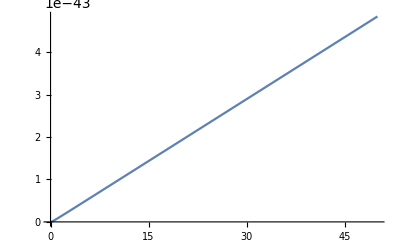

```mathematica
Plot[197.3269804 10^-13*197.3269804 10^-13XESe[Ev],{Ev,0,50}]
```

```mathematica
(*kinematics p+k0=p'+k where p=(me,0), k0=(Ev,Ev n), k=(Ee, pe m)*)
```

```mathematica
Solve[(me+Ev-Ee)^2-(Ev^2+(Ee^2-me^2)-2 Ev √(Ee^2-me^2) cosEs)==0,Ev]
```

{{Ev→(Ee me-me^2)/(-Ee+me+cosEs √(Ee^2-me^2))}}

```mathematica
(*Requiring that Ev>0 and Ee>me, we obtain a bound for the scattering angle*)
```

```mathematica
Reduce[(Ee me-me^2)/(-Ee+me+cosEs √(Ee^2-me^2))>0&&Ee>me&&me>0,cosEs]
```

Ee>0&&0<me<Ee&&cosEs>√((Ee-me)/(Ee+me))

```mathematica
(*Since Ee>me, the scattering angle is always in the forward-cone*)
```

```mathematica
(*From the conservation of the 0th component*)
```

```mathematica
Ev+me==Ev'+Ee
```

```mathematica
(*Formulas for the positron energy Ee*)
```

```mathematica
Solve[(me+Ev-Ee)^2-(Ev^2+(Ee^2-me^2)-2 Ev √(Ee^2-me^2) cosEs)==0,Ee]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{Ee→me},{Ee→(me (Ev^2+cosEs^2 Ev^2+2 Ev me+me^2))/(Ev^2-cosEs^2 Ev^2+2 Ev me+me^2)}}

```mathematica
(*Formula for the scattering angle*)
```

```mathematica
Solve[(me+Ev-Ee)^2-(Ev^2+(Ee^2-me^2)-2 Ev √(Ee^2-me^2) cosEs)==0,cosEs]
```

{{cosEs→(Ee Ev+Ee me-Ev me-me^2)/(Ev √(Ee^2-me^2))}}

```mathematica
(Ee Ev+Ee me-Ev me-me^2)/(Ev √(Ee^2-me^2))//FullSimplify
```

(√((Ee-me) (Ee+me)) (Ev+me))/(Ev (Ee+me))

```mathematica
(*Considering that Ee is always greater than me, we see that the scattering angle has a positive cosine. Then the scattering always takes place in the forward cone*)
```

```mathematica
(*To obtain the neutrino flux (differential in Ev) from the supernova as a spectrum differential in the cosine of the scattering angle we need to compute the jacobian of the function Ev=(Ee me-me^2)/(-Ee+me+cosEs √(Ee^2-me^2))*)
```

```mathematica
D[(Ee me-me^2)/(-Ee+me+cosEs √(Ee^2-me^2)),cosEs]//FullSimplify
```

(me (-Ee+me) √((Ee-me) (Ee+me)))/(-Ee+me+cosEs √((Ee-me) (Ee+me)))^2

```mathematica
(*which can be put in the form (me (-Ee+me) √((Ee-me) (Ee+me)))/(-Ee+me+cosEs √((Ee-me) (Ee+me)))^2*(me(-Ee+me))/(me(-Ee+me)). Then we take the absolute value. *)
```

```mathematica
jacobianES[Ev_,Ee_]:=Ev^2/me*√((Ee+me)/(Ee-me));
```

```mathematica
(*for later convenience, we express the cosine of the scattering angle in terms of Ev and Ee*)
```

```mathematica
cosScatteringAngle[Ev_,Ee_]:=√((Ee-me)/(Ee+me))((Ev+me)/Ev);
```

```mathematica
Plot3D[√((Ee-me)/(Ee+me))((Ev+me)/Ev),{Ee,5,60},{Ev,5,60}]
```

-Graphics3D-

```mathematica
(*We also compute EeMAX and EeMIN*)
```

```mathematica
EeMIN[Ev_]:=me (*corresponding to cosEs=0*)
```

```mathematica
EeMAX[Ev_]:=(2 Ev^2+2 Ev me+me^2)/(2 Ev +me); (*corresponding to cosEs=1*)
```

```mathematica
(*It is also important to compute the minimum neutrino energy that can produce a fixed energy Ee for the electron*)
```

```mathematica
(*The kinetic energy of the scattered electron is*)
```

```mathematica
FullSimplify[(me (Ev^2+cosEs^2 Ev^2+2 Ev me+me^2))/(Ev^2-cosEs^2 Ev^2+2 Ev me+me^2)-me]
```

(2 cosEs^2 Ev^2 me)/(-((-1+cosEs^2) Ev^2)+2 Ev me+me^2)

```mathematica
Te[Ev_,cosEs_]:= (2 cosEs^2 Ev^2 me)/(-cosEs^2 Ev^2+(Ev+me)^2)
```

```mathematica
(*From here we obtain that the maximum kinetic energy is obtain from the forward scattering, cosEs=1*)
```

```mathematica
TeMax[Ev_]:=(2  Ev^2 me)/(- Ev^2+(Ev+me)^2);
```

```mathematica
(*Plot of the scattering angle as function of the incoming neutrino energy as Ee=20 MeV*)
```

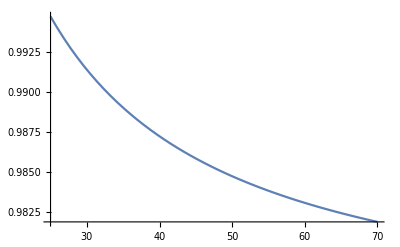

```mathematica
Plot[√((20-me)/(20+me))((Ev+me)/Ev)/.me->0.511,{Ev,25,70}]
```

## Signal for the elastic scattering (normal hierarchy)

### Neutronization Flux

```mathematica
ξ=5;
```

```mathematica
MaxLuminosity=4*10^53/(1.602*10^-6);(*MeV/s*)
AverageEnergy=13;(*MeV*)
Tn=AverageEnergy/(1+ξ);
```

```mathematica
Pee=2.2*10^-2; (*surviving probability of an electronic neutrino*)
```

```mathematica
(*we assume that the flux is constant in time and equal to its maximum value. The temporal shape can be reproduced by means of the function F calligraphic with parameters t0=2.5ms τn=8.2ms n=α=2, corresponding to a total duration of 7.5ms*)
```

```mathematica
NeutronizationFlux[Ev_]:=1/(4 π d^2)*MaxLuminosity/AverageEnergy*Ev^ξ/Tn^(1+ξ)*Exp[-Ev/Tn]/Gamma[1+ξ]; (*I am not sure about the constants before the formula of the flux*)
```

```mathematica
NeutronizationFlux[13]
```

4.50342×10^9

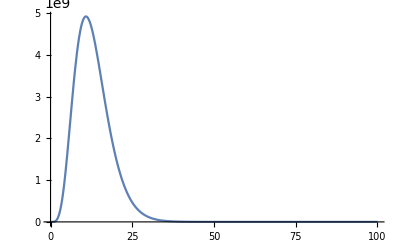

```mathematica
Plot[NeutronizationFlux[Ev],{Ev,0,100},PlotRange->All]
```

### Angular Smearing function

```mathematica
θi=Pi/180*18;
```

```mathematica
δθi=Pi/180*18;
```

```mathematica
δni=0.424 δθi (1-δθi^2/24);
```

```mathematica
N2=1-(1+2/δni)Exp[-2/δni];
```

```mathematica
(*In the following c is the cosine of the angle between the true emission direction and the recostruceted one*)
```

```mathematica
AngularSmearing[cos_]:=1/(N2 δni^2)*Exp[-(√(2(1-cos)))/δni];
```

```mathematica
NIntegrate[AngularSmearing[x],{x,-1,1}]
```

1.

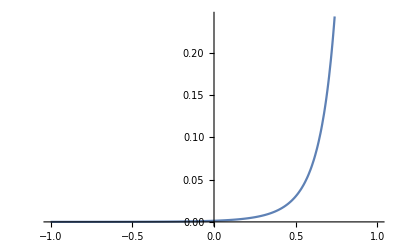

```mathematica
Plot[AngularSmearing[cos],{cos,-1,1}]
```

```mathematica
(*the cosine between the true and the recostucted direction can be expressed in terms of the scattering angle*)
```

```mathematica
cosSmearing=cosScattering*Cos[θi]+√(1-cosScattering^2)*√(1-Cos[θi]^2)*Cos[ϕ];
```

### Definitions of the f functions for the neutronization phase

```mathematica
Cos[18*π/180]//N
```

0.951057

```mathematica
ne=7.15*10^32; (*numero di elettroni in Kamiokande*)
```

```mathematica
(*we assume that the flux is constant in time and equal to its maximum value. The temporal shape can be reproduced by means of the function F calligraphic with parameters t0=2.5ms τn=8.2ms n=α=2, corresponding to a total duration of 7.5ms*)
```

```mathematica
SpectrumNeutronization[Ee_,cosSctr_]:=ne*NeutronizationFlux[(Ee me-me^2)/(-Ee+me+cosSctr √(Ee^2-me^2))]*Pee*dXESe[(Ee me-me^2)/(-Ee+me+cosSctr √(Ee^2-me^2)),Ee]*jacobianES[(Ee me-me^2)/(-Ee+me+cosSctr √(Ee^2-me^2)),Ee]+ne*NeutronizationFlux[(Ee me-me^2)/(-Ee+me+cosSctr √(Ee^2-me^2))]*(1-Pee)*dXESmu[(Ee me-me^2)/(-Ee+me+cosSctr √(Ee^2-me^2)),Ee]*jacobianES[(Ee me-me^2)/(-Ee+me+cosSctr √(Ee^2-me^2)),Ee];
```

```mathematica
SpectrumNeutronizationSmeared[Ei_,cosSctri_,Ee_,cosScattering_,ϕ_]:=1/(2π)*etaK[Ee]*GK[Ee,Ei]*AngularSmearing[cosScattering*Cos[θi]+√(1-cosScattering^2)*√(1-Cos[θi]^2)*Cos[ϕ]]*SpectrumNeutronization[Ee,cosScattering]*MeVbarn*Barncmsquared;
```

```mathematica
SpectrumoNeutronizationEvent[Ei_,cosen_]:=NIntegrate[SpectrumNeutronizationSmeared[Ei,cosen,Ee,cosScattering,ϕ],{Ee,2.61,10,20,50,70},{cosScattering,√((Ee-me)/(Ee+me)),1},{ϕ,0,2π}];
```

```mathematica
SpectrumoNeutronizationEvent[20,0.9510565162951535]
```

0.0383277

## Signal for the elastic scattering (inverted hierarchy)

### Neutronization Flux

```mathematica
ξ=5;
```

```mathematica
MaxLuminosity=4*10^53/(1.602*10^-6);(*MeV/s*)
AverageEnergy=13;(*MeV*)
Tn=AverageEnergy/(1+ξ);
```

```mathematica
Pee=0.296; (*surviving probability of an electronic neutrino*)
```

```mathematica
(*we assume that the flux is constant in time and equal to its maximum value. The temporal shape can be reproduced by means of the function F calligraphic with parameters t0=2.5ms τn=8.2ms n=α=2, corresponding to a total duration of 7.5ms*)
```

```mathematica
NeutronizationFlux[Ev_]:=1/(4 π d^2)*MaxLuminosity/AverageEnergy*Ev^ξ/Tn^(1+ξ)*Exp[-Ev/Tn]/Gamma[1+ξ]; (*I am not sure about the constants before the formula of the flux*)
```

```mathematica
Plot[NeutronizationFlux[Ev],{Ev,0,100},PlotRange->All]
```

-Graphics-

### Angular Smearing function

```mathematica
θi=Pi/180*18;
```

```mathematica
δθi=Pi/180*18;
```

```mathematica
δni=0.424 δθi (1-δθi^2/24);
```

```mathematica
N2=1-(1+2/δni)Exp[-2/δni];
```

```mathematica
(*In the following c is the cosine of the angle between the true emission direction and the recostruceted one*)
```

```mathematica
AngularSmearing[cos_]:=1/(N2 δni^2)*Exp[-(√(2(1-cos)))/δni];
```

```mathematica
NIntegrate[AngularSmearing[x],{x,-1,1}]
```

1.

```mathematica
Plot[AngularSmearing[cos],{cos,-1,1}]
```

-Graphics-

```mathematica
(*the cosine between the true and the recostucted direction can be expressed in terms of the scattering angle*)
```

```mathematica
cosSmearing=cosScattering*Cos[θi]+√(1-cosScattering^2)*√(1-Cos[θi]^2)*Cos[ϕ];
```

### Definitions of the f functions for the neutronization phase

```mathematica
ne=7.15*10^32; (*numero di elettroni in Kamiokande*)
```

```mathematica
(*we assume that the flux is constant in time and equal to its maximum value. The temporal shape can be reproduced by means of the function F calligraphic with parameters t0=2.5ms τn=8.2ms n=α=2, corresponding to a total duration of 7.5ms*)
```

```mathematica
SpectrumNeutronization[Ee_,cosSctr_]:=ne*NeutronizationFlux[(Ee me-me^2)/(-Ee+me+cosSctr √(Ee^2-me^2))]*Pee*dXESe[(Ee me-me^2)/(-Ee+me+cosSctr √(Ee^2-me^2)),Ee]*jacobianES[(Ee me-me^2)/(-Ee+me+cosSctr √(Ee^2-me^2)),Ee]+ne*NeutronizationFlux[(Ee me-me^2)/(-Ee+me+cosSctr √(Ee^2-me^2))]*(1-Pee)*dXESmu[(Ee me-me^2)/(-Ee+me+cosSctr √(Ee^2-me^2)),Ee]*jacobianES[(Ee me-me^2)/(-Ee+me+cosSctr √(Ee^2-me^2)),Ee];
```

```mathematica
SpectrumNeutronizationSmeared[Ei_,cosSctri_,Ee_,cosScattering_,ϕ_]:=1/(2π)*etaK[Ee]*GK[Ee,Ei]*AngularSmearing[cosScattering*Cos[θi]+√(1-cosScattering^2)*√(1-Cos[θi]^2)*Cos[ϕ]]*SpectrumNeutronization[Ee,cosScattering]*MeVbarn*Barncmsquared;
```

```mathematica
SpectrumoNeutronizationEvent[Ei_,cosen_]:=NIntegrate[SpectrumNeutronizationSmeared[Ei,cosen,Ee,cosScattering,ϕ],{Ee,2.61,10,20,50,70},{cosScattering,√((Ee-me)/(Ee+me)),1},{ϕ,0,2π}];
```

```mathematica
SpectrumoNeutronizationEvent[20,0.9510565162951535]
```

0.0995357